```mathematica
(* set-up *)
vec1[A1_,A2_]:=-(M0*A1+N0*A2^2+K0*A1^3+2*K2*A1*A2^2)
vec2[A1_,A2_]:=-(M0*A2+N0*A1*A2+(K0+K2)*A2^3+K2*A2*A1^2)
```

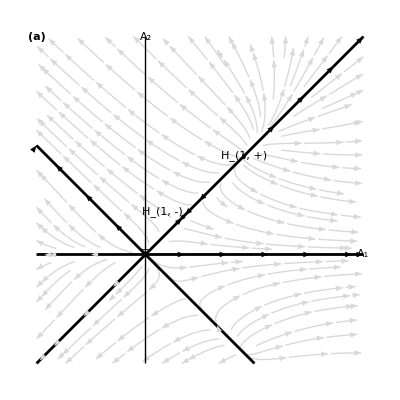

```mathematica
(* plot for M0 < 0 *)
N0=1;
K0=-1;
K2=-3.5;
M0=-0.025;
(* fixed points *)
hexPlus={(-N0-Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2)),(-N0-Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2))};
hexMinus={(-N0+Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2)),(-N0+Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2))};
line1=Line[{{0,-0.1},{0,0.2}}];
fig=Plot[{x,0},{x,-0.1,0.2},PlotStyle->Black,Ticks->None];
fig2=Plot[-x,{x,-0.1,0.1},PlotStyle->Black,Ticks->None];
vecfield=StreamPlot[{(-M0*x-N0*y^2-K0*x^3-2*K2*x*y^2),(-M0*y-N0*x*y-(K0+K2)*y^3-K2*y*x^2)},{x,-0.1,0.2},{y,-0.1,0.2},Epilog->{Black,PointSize[Large],Point[{hexPlus,{0,0},hexMinus}],Text[Style[" H_(1, +) ",Italic,Larger],hexPlus,{1,-2},Background->White],Text[Style[" T ",Italic,Larger],{0,0},{1.5,2},Background->White],Text[Style[" H_(1, -)",Italic,Larger],hexMinus,{1.5,-1},Background->White],Text[Style[" (a) ",Bold,Larger],{-0.1,0.2},{-2,2},Background->White],
Text[Style["A_1",Italic,Larger],{0.2,0},{0,-1.5},Background->White],
Text[Style["A_2",Italic,Larger],{0,0.2},{-1.5,0},Background->White],
line1},
StreamColorFunction->None,
StreamStyle->LightGray,
StreamScale->0.12,
StreamPoints->{{{{0.2,0},Black},
			{{0.2,0.2},Black},
			{{0.075,0.075},Black},
			{{-0.1,0.1},Black},
			{{0.008,0.008},Black},
			Automatic}},
FrameTicks->None,Frame->False];
figure=Show[vecfield,fig,fig2]
```

0.707107

0

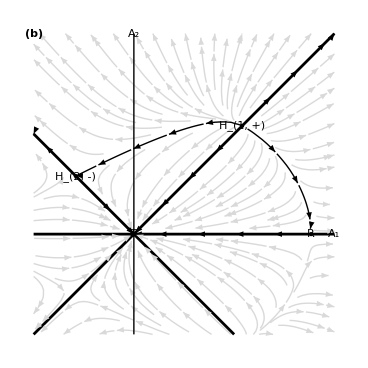

```mathematica
(* plot 1 for M0 > 0 *)
M0=0.5;
N0=1;
K0=-1;
K2=-2;
xRoll=Sqrt[-M0/K0]
yRoll=0
hexPlus={(-N0-Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2)),(-N0-Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2))};
hexMinus={(-N0+Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2)),-(-N0+Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2))};
line1=Line[{{0,-0.4},{0,0.8}}];
fig=Plot[{x,0},{x,-0.4,0.8},PlotStyle->Black,Ticks->None];
fig2=Plot[-x,{x,-0.4,0.4},PlotStyle->Black,Ticks->None];
vecfield=StreamPlot[{-M0*x-N0*y^2-K0*x^3-2*K2*x*y^2,-M0*y-N0*x*y-(K0+K2)*y^3-K2*y*x^2},{x,-0.4,0.8},{y,-0.4,0.8},Epilog->{Black,PointSize[Large],Point[{hexPlus,{xRoll,yRoll},{0,0},hexMinus}],Text[Style[" R ",Italic,Larger],{xRoll,yRoll},{0,2},Background->White],Text[Style[" H_(1, +) ",Italic,Larger],hexPlus,{1,-2},Background->White],Text[Style[" T ",Italic,Larger],{0,0},{1.5,2},Background->White],Text[Style[" H_(2, -)",Italic,Larger],hexMinus,{1.7,0},Background->White],Text[Style[" (b) ",Bold,Larger],{-0.4,0.8},{-2,2},Background->White],
Text[Style["A_1",Italic,Larger],{0.8,0},{0,-1.5},Background->White],
Text[Style["A_2",Italic,Larger],{0,0.8},{-1.5,0},Background->White],
line1},
StreamColorFunction->None,
StreamStyle->LightGray,
StreamScale->0.12,
StreamPoints->{{{{0.5,0},Black},
			{{0.2,0.2},Black},
			{{0.69428,0.1},Black},
			{{-0.09125,0.3},Black},
			{{0.8,0.8},Black},
			{{-0.1,0.1},Black},
			{{-0.4,0.4},Black},
			{{0.8,0.8},Black},
			Automatic}},
FrameTicks->None,Frame->False];
figure=Show[vecfield,fig,fig2]
```

{{0.36,0.455368},{0.227684,0.144}}

{{0.891322,0.453372},{-0.713145,0.701016}}

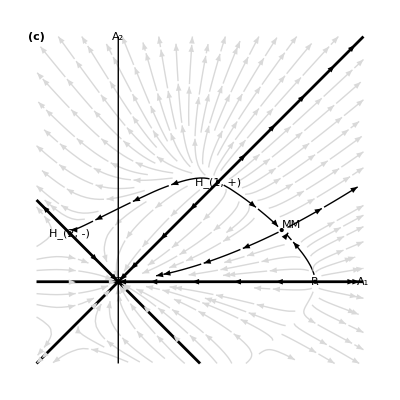

```mathematica
(* plot 2 for M0 > 0 *)
N0=1;
K0=-1;
K2=-3.5;
λ=0.9;
M0=λ*(-K0*N0^2/(K0-K2)^2)+(1-λ)*(-N0^2*(2*K0+K2)/(K0-K2)^2);
(* fixed points *)
xRoll=Sqrt[-M0/K0];
yRoll=0;
hexPlus={(-N0-Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2)),(-N0-Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2))};
hexMinus={(-N0+Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2)),-(-N0+Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2))};
mm={N0/(K0-K2),(1/(K0-K2))*Sqrt[-(K0*N0^2+(K0-K2)^2*M0)/(K0+K2)]};
lin={{D[vec1[a1,a2],a1],D[vec1[a1,a2],a2]},
{D[vec2[a1,a2],a1],D[vec2[a1,a2],a2]}}/.{a1->mm[[1]],a2->mm[[2]]}
Eigenvectors[lin]
line1=Line[{{0,-0.2},{0,0.6}}];
fig=Plot[{x,0},{x,-0.2,0.6},PlotStyle->Black,Ticks->None];
fig2=Plot[-x,{x,-0.2,0.2},PlotStyle->Black,Ticks->None];
vecfield=StreamPlot[{(-M0*x-N0*y^2-K0*x^3-2*K2*x*y^2),(-M0*y-N0*x*y-(K0+K2)*y^3-K2*y*x^2)},{x,-0.2,0.6},{y,-0.2,0.6},Epilog->{Black,PointSize[Large],Point[{hexPlus,{xRoll,yRoll},{0,0},hexMinus,mm}],Text[Style[" R ",Italic,Larger],{xRoll,yRoll},{0,2},Background->White],Text[Style[" H_(1, +) ",Italic,Larger],hexPlus,{1,-2},Background->White],Text[Style[" T ",Italic,Larger],{0,0},{1.5,2},Background->White],Text[Style[" H_(2, -)",Italic,Larger],hexMinus,{1.7,0},Background->White],Text[Style[" MM ",Italic,Larger],mm,{-0.5,-3},Background->White],Text[Style[" (c) ",Bold,Larger],{-0.2,0.6},{-2,2},Background->White],
Text[Style["A_1",Italic,Larger],{0.6,0},{0,-1.5},Background->White],
Text[Style["A_2",Italic,Larger],{0,0.6},{-1.5,0},Background->White],
line1},
StreamColorFunction->None,
StreamStyle->LightGray,
StreamScale->0.12,
StreamPoints->{{{{0.2,0},Black},
			{{0.5,0},Black},
			{{0.2,0.2},Black},
			{{0.5,0.5},Black},
			{{-0.15,0.15},Black},
			{{-0.1,0.1},Black},
			{{0.3,0.20967558986},Black},
			{{0.45,0.0704364},Black},
			{{0.1,0.2259},Black},
			{mm+0.05*{0.8913216364346908,0.45337152581893},Black},
			{mm-0.05*{0.8913216364346908,0.45337152581893},Black},
			Automatic}},
FrameTicks->None,Frame->False];
figure=Show[vecfield,fig,fig2]
```

{{11.8311,7.72487},{3.86243,41.44}}

{{-0.244885,-0.969552},{-0.99212,0.125292}}

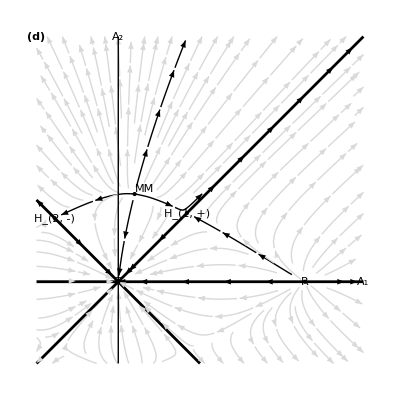

```mathematica
(* plot 3 for M0 > 0 *)
N0=1;
K0=-1;
K2=-3.5;
λ=0.9;
M0=(-N0^2*(2*K0+K2)/(K0-K2)^2)+20;
(* fixed points *)
xRoll=Sqrt[-M0/K0];
yRoll=0;
hexPlus={(-N0-Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2)),(-N0-Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2))};
hexMinus={(-N0+Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2)),-(-N0+Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2))};
mm={N0/(K0-K2),(1/(K0-K2))*Sqrt[-(K0*N0^2+(K0-K2)^2*M0)/(K0+K2)]};
lin={{D[vec1[a1,a2],a1],D[vec1[a1,a2],a2]},
{D[vec2[a1,a2],a1],D[vec2[a1,a2],a2]}}/.{a1->mm[[1]],a2->mm[[2]]}
Eigenvectors[lin]
line1=Line[{{0,-2},{0,6}}];
fig=Plot[{x,0},{x,-2,6},PlotStyle->Black,Ticks->None];
fig2=Plot[-x,{x,-2,2},PlotStyle->Black,Ticks->None];
vecfield=StreamPlot[{(-M0*x-N0*y^2-K0*x^3-2*K2*x*y^2),(-M0*y-N0*x*y-(K0+K2)*y^3-K2*y*x^2)},{x,-2,6},{y,-2,6},Epilog->{Black,PointSize[Large],Point[{hexPlus,{xRoll,yRoll},{0,0},hexMinus,mm}],Text[Style[" R ",Italic,Larger],{xRoll,yRoll},{0,2},Background->White],Text[Style[" H_(1, +) ",Italic,Larger],hexPlus,{-2,-0.2},Background->White],Text[Style[" T ",Italic,Larger],{0,0},{1.5,2},Background->White],Text[Style[" H_(2, -)",Italic,Larger],hexMinus,{1.7,0},Background->White],Text[Style[" MM ",Italic,Larger],mm,{-1.5,-1.5},Background->White],Text[Style[" (d) ",Bold,Larger],{-2,6},{-2,2},Background->White],
Text[Style["A_1",Italic,Larger],{6,0},{0,-1.5},Background->White],
Text[Style["A_2",Italic,Larger],{0,6},{-1.5,0},Background->White],
line1},
StreamColorFunction->None,
StreamStyle->LightGray,
StreamScale->0.12,
StreamPoints->{{{{0.2,0},Black},
			{{4.8,0},Black},
			{{0.2,0.2},Black},
			{{3,3},Black},
			{{-2,2},Black},
			{{-1,1},Black},
			{hexPlus-0.09*{2,-1},Black},
			{hexMinus+0.1*{2,1},Black},
			{hexPlus+0.1*{2,-1},Black},
			{{0.1,0.2259},Black},
			{mm-0.2*{-0.24488474353124945,-0.9695521968339992},Black},
			{mm+0.2*{-0.24488474353124945,-0.9695521968339992},Black},
			Automatic}},
FrameTicks->None,Frame->False];
figure=Show[vecfield,fig,fig2]
```

{{vec1^(1,0)[0.4,1.54344],vec1^(0,1)[0.4,1.54344]},{vec2^(1,0)[0.4,1.54344],vec2^(0,1)[0.4,1.54344]}}

{{-1/(2 vec2^(1,0)[0.4,1.54344])(vec2^(0,1)[0.4,1.54344]-vec1^(1,0)[0.4,1.54344]+√((vec2^(0,1)[0.4,1.54344])^2-2 vec2^(0,1)[0.4,1.54344] vec1^(1,0)[0.4,1.54344]+(vec1^(1,0)[0.4,1.54344])^2+4 vec1^(0,1)[0.4,1.54344] vec2^(1,0)[0.4,1.54344])),1},{-1/(2 vec2^(1,0)[0.4,1.54344])(vec2^(0,1)[0.4,1.54344]-vec1^(1,0)[0.4,1.54344]-√((vec2^(0,1)[0.4,1.54344])^2-2 vec2^(0,1)[0.4,1.54344] vec1^(1,0)[0.4,1.54344]+(vec1^(1,0)[0.4,1.54344])^2+4 vec1^(0,1)[0.4,1.54344] vec2^(1,0)[0.4,1.54344])),1}}

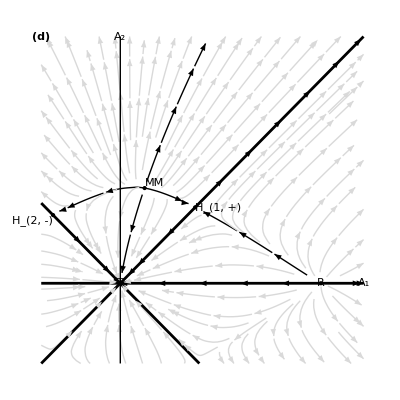

```mathematica
(* alternative plot 3 for M0 > 0 *)
N0=1;
K0=-1;
K2=-3.5;
λ=0.9;
M0=(-N0^2*(2*K0+K2)/(K0-K2)^2)+10;
(* fixed points *)
xRoll=Sqrt[-M0/K0];
yRoll=0;
hexPlus={(-N0-Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2)),(-N0-Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2))};
hexMinus={(-N0+Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2)),-(-N0+Sqrt[N0^2-4*M0*(K0+2*K2)])/(2*(K0+2*K2))};
mm={N0/(K0-K2),(1/(K0-K2))*Sqrt[-(K0*N0^2+(K0-K2)^2*M0)/(K0+K2)]};
lin={{D[vec1[a1,a2],a1],D[vec1[a1,a2],a2]},
{D[vec2[a1,a2],a1],D[vec2[a1,a2],a2]}}/.{a1->mm[[1]],a2->mm[[2]]}
Eigenvectors[lin]
line1=Line[{{0,-1.3},{0,4}}];
fig=Plot[{x,0},{x,-1.3,4},PlotStyle->Black,Ticks->None];
fig2=Plot[-x,{x,-1.3,1.3},PlotStyle->Black,Ticks->None];
vecfield=StreamPlot[{(-M0*x-N0*y^2-K0*x^3-2*K2*x*y^2),(-M0*y-N0*x*y-(K0+K2)*y^3-K2*y*x^2)},{x,-1.3,4},{y,-1.3,4},Epilog->{Black,PointSize[Large],Point[{hexPlus,{xRoll,yRoll},{0,0},hexMinus,mm}],Text[Style[" R ",Italic,Larger],{xRoll,yRoll},{0,2},Background->White],Text[Style[" H_(1, +) ",Italic,Larger],hexPlus,{-2.1,-0.4},Background->White],Text[Style[" T ",Italic,Larger],{0,0},{1.5,2},Background->White],Text[Style[" H_(2, -)",Italic,Larger],hexMinus,{1,1.7},Background->White],Text[Style[" MM ",Italic,Larger],mm,{-1.7,-1.7},Background->White],Text[Style[" (d) ",Bold,Larger],{-1.3,4},{-2,2},Background->White],
Text[Style["A_1",Italic,Larger],{4,0},{0,-1.5},Background->White],
Text[Style["A_2",Italic,Larger],{0,4},{-1.5,0},Background->White],
line1},
StreamColorFunction->None,
StreamStyle->LightGray,
StreamScale->0.12,
StreamPoints->{{{0.2,0},Black},
			{{3.8,0},Black},
			{{0.2,0.2},Black},
			{{3,3},Black},
			{{-2,2},Black},
			{{-1,1},Black},
			{hexPlus-0.07*{2,-1},Black},
			{hexMinus+0.1*{2,1},Black},
			{hexPlus+0.06*{2,-1},Black},
			{mm-0.2*{-0.32583920070089595,-0.9454252034331437},Black},
			{mm+0.2*{-0.32583920070089595,-0.9454252034331437},Black},
			Automatic},
FrameTicks->None,Frame->False];
figure=Show[vecfield,fig,fig2]
```